```mathematica
(*dir ="/Users/laik/Documents/fall2022/Images/locule_scans/cropped/";*)
filename ="lalo82";
(*img =Import[dir <> filename <> ".JPG"];
crans=img;*)
crans = -Graphics-;
```

```mathematica
sizeCircle=-Graphics-;
(*1 inch diameter, cropped from the same image as the cranberries above so pixel count is the same scale*)
binSizeCircle = ColorNegate[Binarize[sizeCircle]];
countTotal = Total[binSizeCircle]
diameterOfSizeCircle = Max[Total /@ ImageData[binSizeCircle]];
(diameterOfSizeCircle / 2.0) ^ 2 * Pi
trueSize = (0.5)^2*Pi

convertPixelsToInSquared = trueSize / countTotal
```

281675.

281802.

0.785398

2.78831×10^-6

```mathematica
(*Increase the contrast to better see the hollow areas*)
ContrastCrans = ImageAdjust[crans,5];
(*Use the kuwahara filter to smooth the colors while preserving edges*)
KuwaCrans = KuwaharaFilter[ContrastCrans, 5]
```

-Graphics-

```mathematica
(*Binarize at different treshold values, add the results together because some holes show up better at different levels.
Use the Watershed segmentation method to get the segments of the image that are the hollow locules.
Do each color channel individually because each color channel also has different holes. 
The masks are all added together to create one final mask of the inner hollow area.
This method was invented purely through experimentation of different values and noticing what worked best*)
BinCrans = Binarize[ColorSeparate[ContrastCrans][[1]],#]&/@Range[0,1, 0.05];
mask1 = Total[ColorNegate[Binarize[Colorize[WatershedComponents[#,Method->{"MinimumSaliency",0.3}]]]]&/@BinCrans];
mask1 = DeleteSmallComponents[mask1, 200];
```

```mathematica
BinCrans = Binarize[ColorSeparate[ContrastCrans][[2]],#]&/@Range[0,1, 0.05];
mask2 = Total[ColorNegate[Binarize[Colorize[WatershedComponents[#,Method->{"MinimumSaliency",0.3}]]]]&/@BinCrans];
mask2 = DeleteSmallComponents[mask2, 200];
```

```mathematica
BinCrans = Binarize[ColorSeparate[ContrastCrans][[3]],#]&/@Range[0,1, 0.05];
mask3 = Total[ColorNegate[Binarize[Colorize[WatershedComponents[#,Method->{"MinimumSaliency",0.3}]]]]&/@BinCrans];
mask3 = DeleteSmallComponents[mask3, 200];
```

```mathematica
mask = mask1+mask2+mask3
```

-Graphics-

```mathematica
(*Create mask of stamp/footprint of the full cranberry slice*)
fullCranContours = ContourDetect[crans, 0.2];
fullCranContours + mask;
finalCranMask = DeleteSmallComponents[ColorNegate[fullCranContours + mask],100]
```

-Graphics-

```mathematica
(*Partition the image into each individual cranberry to calculate data about each cranberry*)
origCransPartition = Flatten[ImagePartition[crans,{ImageDimensions[crans][[1]]/5, ImageDimensions[crans][[2]]/5}]];
```

```mathematica
cranPartition =Flatten[ImagePartition[finalCranMask,{ImageDimensions[finalCranMask][[1]]/5, ImageDimensions[finalCranMask][[2]]/5}]];
```

```mathematica
fullCranPartition = Flatten[ImagePartition[DeleteSmallComponents[ColorNegate[fullCranContours], 100],{ImageDimensions[fullCranContours][[1]]/5, ImageDimensions[fullCranContours][[2]]/5}]];
```

```mathematica
hollowCranSizes = Total /@ Flatten /@ImageData /@ cranPartition;
fullCranSizes =  Total /@ Flatten /@ImageData /@ fullCranPartition;
```

```mathematica
(*Average color*)
averageCranColor = Range[Length[origCransPartition]];
Do[
averageCranColor[[i]] = ImageMeasurements[origCransPartition[[i]], "Mean",  Masking -> fullCranPartition[[i]]];
,{i,1,Length[averageCranColor]}]
averageCranColor;
shownAvgCranColor =Graphics[{RGBColor[#],Disk[]}] &/@ averageCranColor;
```

```mathematica
(*Convert Sizes*)
fullCranSizesInchesSquared = convertPixelsToInSquared * fullCranSizes;
hollowCranSizesInchesSquared = convertPixelsToInSquared * hollowCranSizes;
```

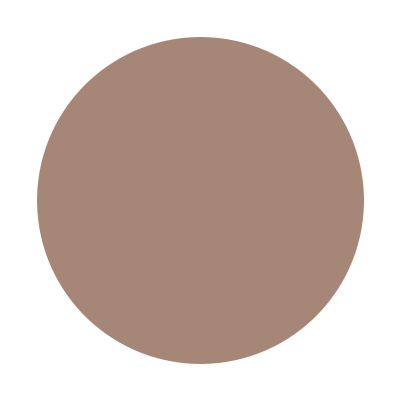
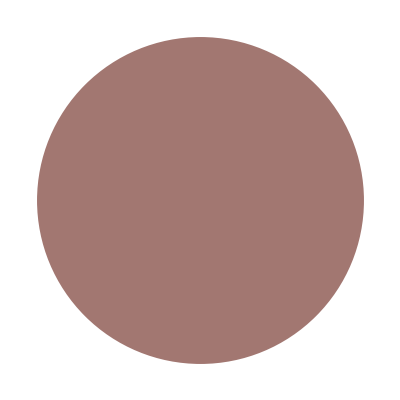
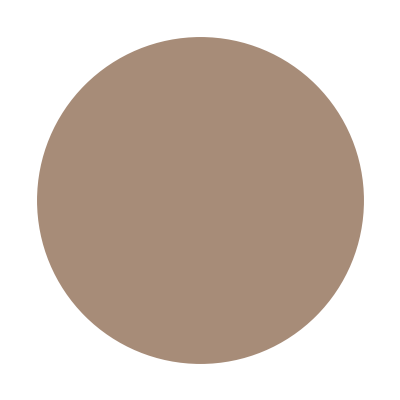
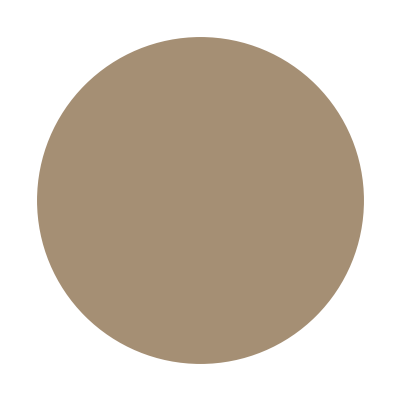
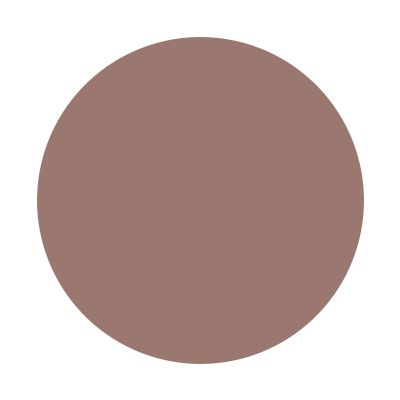
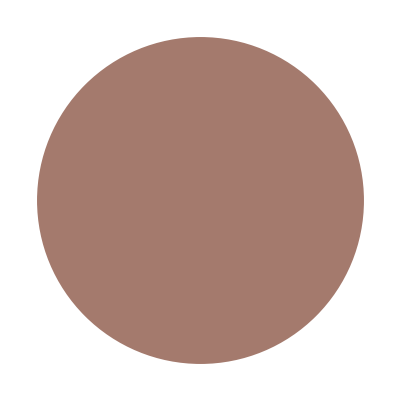
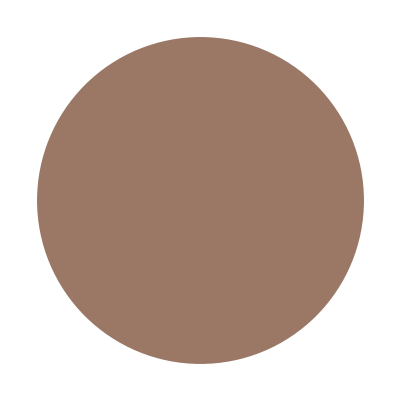
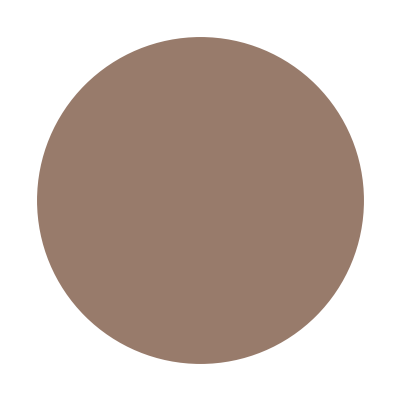
(Original | Avg. Color | Avg. Color (RGB 0-1) | Mask | Total area | Hollow area | Non-hollow area
-Graphics- | -Graphics- | {0.649944,0.525314,0.464957} | -Graphics- | 0.200477 | 0.0532373 | 0.14724
-Graphics- | -Graphics- | {0.634189,0.467539,0.443274} | -Graphics- | 0.21434 | 0.0868504 | 0.12749
-Graphics- | -Graphics- | {0.653099,0.547146,0.469371} | -Graphics- | 0.245935 | 0.0791491 | 0.166786
-Graphics- | -Graphics- | {0.647544,0.559995,0.45342} | -Graphics- | 0.258011 | 0.0646694 | 0.193342
-Graphics- | -Graphics- | {0.602924,0.471059,0.436061} | -Graphics- | 0.206868 | 0.0732518 | 0.133616
-Graphics- | -Graphics- | {0.642357,0.479036,0.429232} | -Graphics- | 0.204342 | 0.0894128 | 0.114929
-Graphics- | -Graphics- | {0.606362,0.469248,0.401419} | -Graphics- | 0.290668 | 0.101645 | 0.189023
-Graphics- | -Graphics- | {0.595119,0.481459,0.420862} | -Graphics- | 0.137935 | 0.0405644 | 0.0973707
-Graphics- | -Graphics- | {0.616487,0.493284,0.428991} | -Graphics- | 0.229724 | 0.0911193 | 0.138604
-Graphics- | -Graphics- | {0.628636,0.508418,0.435542} | -Graphics- | 0.194541 | 0.0708009 | 0.12374
-Graphics- | -Graphics- | {0.632914,0.534203,0.460011} | -Graphics- | 0.259885 | 0.104344 | 0.15554
-Graphics- | -Graphics- | {0.636952,0.489916,0.445871} | -Graphics- | 0.260632 | 0.0748941 | 0.185738
-Graphics- | -Graphics- | {0.584325,0.450501,0.422151} | -Graphics- | 0.245726 | 0.0772056 | 0.16852
-Graphics- | -Graphics- | {0.620992,0.495849,0.420335} | -Graphics- | 0.193088 | 0.0639472 | 0.129141
-Graphics- | -Graphics- | {0.638421,0.510822,0.440742} | -Graphics- | 0.154793 | 0.0439243 | 0.110869
-Graphics- | -Graphics- | {0.597668,0.460185,0.406355} | -Graphics- | 0.269496 | 0.102284 | 0.167212
-Graphics- | -Graphics- | {0.640463,0.532633,0.448009} | -Graphics- | 0.234545 | 0.0689884 | 0.165556
-Graphics- | -Graphics- | {0.619028,0.506367,0.452119} | -Graphics- | 0.215124 | 0.0494201 | 0.165704
-Graphics- | -Graphics- | {0.625134,0.526792,0.459227} | -Graphics- | 0.222198 | 0.0860948 | 0.136103
-Graphics- | -Graphics- | {0.645947,0.49587,0.467011} | -Graphics- | 0.23365 | 0.032219 | 0.201431
-Graphics- | -Graphics- | {0.667577,0.548338,0.474125} | -Graphics- | 0.238445 | 0.0666546 | 0.171791
-Graphics- | -Graphics- | {0.62898,0.478359,0.42768} | -Graphics- | 0.212221 | 0.0679763 | 0.144245
-Graphics- | -Graphics- | {0.610019,0.460008,0.397349} | -Graphics- | 0.209943 | 0.0922653 | 0.117678
-Graphics- | -Graphics- | {0.614912,0.467998,0.419296} | -Graphics- | 0.205825 | 0.0711104 | 0.134715
-Graphics- | -Graphics- | {0.611174,0.510098,0.441628} | -Graphics- | 0.177641 | 0.0718186 | 0.105822)

```mathematica
(*Data recorded via some analysis*)
labels = {"Original", "Avg. Color", "Avg. Color (RGB 0-1)", "Mask", "Total area", "Hollow area", "Non-hollow area"};
data =Transpose[{origCransPartition, shownAvgCranColor,averageCranColor,cranPartition, fullCranSizesInchesSquared, fullCranSizesInchesSquared - hollowCranSizesInchesSquared, hollowCranSizesInchesSquared}];
output = (Join[{labels}, data] // MatrixForm)
(*
Original image, mask, total area, hollow area, non-hollow area
*)
```

```mathematica
Export["Documents/fall2022/Output/"<>filename<>".csv",
Join[{{"Full area", "Non-hollow area", "Hollow area", "Avg. Color"}},Transpose[{fullCranSizesInchesSquared, fullCranSizesInchesSquared - hollowCranSizesInchesSquared, hollowCranSizesInchesSquared, averageCranColor}]], 
"csv"]
```

Documents/fall2022/Output/lalo82.csv

```mathematica
img=Rasterize[output];
Export["Documents/fall2022/Output/"<>filename<>"_out.jpg",img]
```

Documents/fall2022/Output/lalo82_out.jpg